# MST

MMAのコードを書き直す必要あり。
-> AcyclicGraphQ[] をつかう。
ひとまず、MMAからMSTを実行し、その結果をImportするラッパーを作成する。

## Dir

```mathematica
(*SetDirectory["/home/kamano/gitsrc/ClusteringAdequation/test-data"]*)
```

```mathematica
(*SetDirectory["/Users/kouamano/gitsrc/ClusteringAdequation/test-data"]*)
```

/Users/kouamano/gitsrc/ClusteringAdequation/test-data

```mathematica
SetDirectory["/Users/amanokou/gitsrc/ClusteringAdequation/test-data"]
```

/Users/amanokou/gitsrc/ClusteringAdequation/test-data

## Program

```mathematica
(*Get["/Users/kouamano/gitsrc/MATH_SCRIPT/SCRIPTS/Network_operations.txt"]*)
```

```mathematica
Get["/Users/amanokou/gitsrc/MATH_SCRIPT/SCRIPTS/Network_operations.txt"]
```

/home/kamano/gitsrc/MATH_SCRIPT/SCRIPTS/Network_operations.txt  に移行。

edge uniq:

```mathematica
(*udEdgeTake[dmat_]:=Sort[Union[Cases[Flatten[MapIndexed[{Sort[#2],#1}&,dmat,{2}],1],{{x_,y_},_}/;x≠y]],#1[[2]]<#2[[2]]&]*)
```

Closeed path test:

```mathematica
(*mstCycleTest[mst_]:=Module[
{nEdge,nNode},
nEdge=Length[mst];
nNode=Length[Union[Flatten[Map[#[[1]]&,mst]]]];
(*{nEdge,nNode}*)
If[nEdge<nNode,True,False]
]*)
```

addOpenPath:

```mathematica
(*mstAddTest[mstANDpoolPos_,edgePool_,size_]:=Module[
{mst,mstNew,poolPos},
mst=mstANDpoolPos[[1]];
poolPos=mstANDpoolPos[[2]];
mstNew=Join[mst,{edgePool[[poolPos+1]]}];
(*mstCycleTest[mst]*)
If[mstCycleTest[mstNew],{mstNew,poolPos+1},{mst,poolPos+1}]
(*{mstNew,poolPos+1,edgePool,size}*)
(*mstNew*)
]*)
```

create first argment:

```mathematica
(*mstCreateFirst[edgePool_]:={{edgePool[[1]]},1}*)
```

get node size:

```mathematica
(*mstEdgePoolSize[edgePool_]:=Max[Flatten[Map[#[[1]]&,edgePool]]]*)
```

MST:

```mathematica
(*MST[edgePool_]:=Module[
{first,size,e},
first=mstCreateFirst[edgePool];
size=mstEdgePoolSize[edgePool];
NestWhile[mstAddTest[#,edgePool,size]&,first,Length[#[[1]]]<size-1&]
]*)
```

```mathematica
(*MSTdmat[dm_]:=Module[
{edgePool,first,size,e},
edgePool=udEdgeTake[dm];
first=mstCreateFirst[edgePool];
size=mstEdgePoolSize[edgePool];
NestWhile[mstAddTest[#,edgePool,size]&,first,Length[#[[1]]]<size-1&]
]*)
```

## Test(1)

list

```mathematica
li={{1,2},{3,4},{2,4},{3,5},{3,9}}
```

{{1,2},{3,4},{2,4},{3,5},{3,9}}

distance matrix

```mathematica
dmli=Outer[EuclideanDistance,li,li,1]//N
```

{{0.,2.82843,2.23607,3.60555,7.28011},{2.82843,0.,1.,1.,5.},{2.23607,1.,0.,1.41421,5.09902},{3.60555,1.,1.41421,0.,4.},{7.28011,5.,5.09902,4.,0.}}

```mathematica
Directory[]
```

/Users/amanokou/gitsrc/ClusteringAdequation/test-data

```mathematica
Export["dm.tsv",dmli]
```

dm.tsv

```mathematica
(*e=Sort[Union[Cases[Flatten[MapIndexed[{Sort[#2],#1}&,dm,{2}],1],{{x_,y_},_}/;x≠y]],#1[[2]]<#2[[2]]&]*)
```

edge uniq:

```mathematica
e=udEdgeTake[dmli]
```

{{{2,4},1.},{{2,3},1.},{{3,4},1.41421},{{1,3},2.23607},{{1,2},2.82843},{{1,4},3.60555},{{4,5},4.},{{2,5},5.},{{3,5},5.09902},{{1,5},7.28011}}



```mathematica
Graph[Map[#[[1]]&,e]]
```

```mathematica
mstCycleTest[e]
```

False

MST :

```mathematica
MST[e]
```

{{{{2,4},1.},{{2,3},1.},{{1,3},2.23607},{{4,5},4.}},7}

```mathematica
Map[#+{{-1,-1},0}&,MSTdmat[dmli][[1]]]
```

{{{1,3},1.},{{1,2},1.},{{0,2},2.23607},{{3,4},4.}}

## Test(2)

```mathematica
dm["iris20"]=Import["iris.20.2.dmat","Table"];
```

```mathematica
(mstMMA=MSTdmat[dm["iris20"]]//MSTreform//Sort)//TableForm
```

1 | 18 | 0
2 | 10 | 0.1
2 | 13 | 0.1
3 | 4 | 0.141421
3 | 12 | 0.223607
4 | 9 | 0.282843
4 | 13 | 0.223607
5 | 18 | 0.141421
5 | 20 | 0.223607
6 | 17 | 0
7 | 12 | 0.2
8 | 12 | 0.2
8 | 18 | 0.141421
9 | 14 | 0.141421
11 | 17 | 0.2
15 | 16 | 0.412311
15 | 19 | 0.223607
17 | 19 | 0.316228
17 | 20 | 0.316228

```mathematica
Map[#[[3]]&,mstMMA]//Tr
```

3.58772

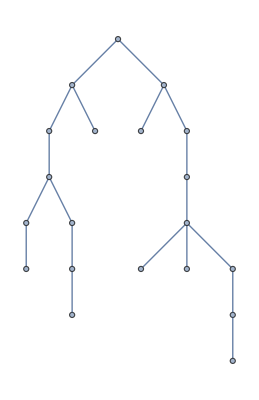

```mathematica
Graph[Map[{#[[1]],#[[2]]}&,mstMMA]]
```

```mathematica
(mstC=Map[MSTBaseShift[#,1]&,Import["iris.20.2.MST","Table"]]//Sort)//TableForm
```

1 | 5 | 0.141421
1 | 8 | 0.141421
1 | 18 | 0.
2 | 13 | 0.1
3 | 4 | 0.141421
3 | 10 | 0.223607
4 | 9 | 0.282843
5 | 20 | 0.223607
6 | 11 | 0.2
6 | 17 | 0.
6 | 19 | 0.316228
7 | 3 | 0.223607
8 | 12 | 0.2
9 | 14 | 0.141421
10 | 2 | 0.1
12 | 7 | 0.2
15 | 16 | 0.412311
19 | 15 | 0.223607
20 | 6 | 0.316228

```mathematica
Map[#[[3]]&,mstC]//Tr
```

3.58772

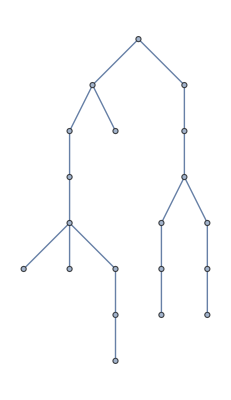

```mathematica
Graph[Map[{#[[1]],#[[2]]}&,mstC]]
```

同じ距離の異なるエッジがあった場合、どれを先に採用するかで結果が異なる。

## Performance

```mathematica
rl=Table[RandomReal[],{150},{2}];
```

```mathematica
rd=Outer[EuclideanDistance,rl,rl,1];
```

```mathematica
Timing[MSTdmat[rd];]
```

{0.34395,Null}